# Analizando los tweets de consulta de @RAEinforma

## Resultado del 15 de Junio de 2019, entre las 17:48 y las 22:04 :

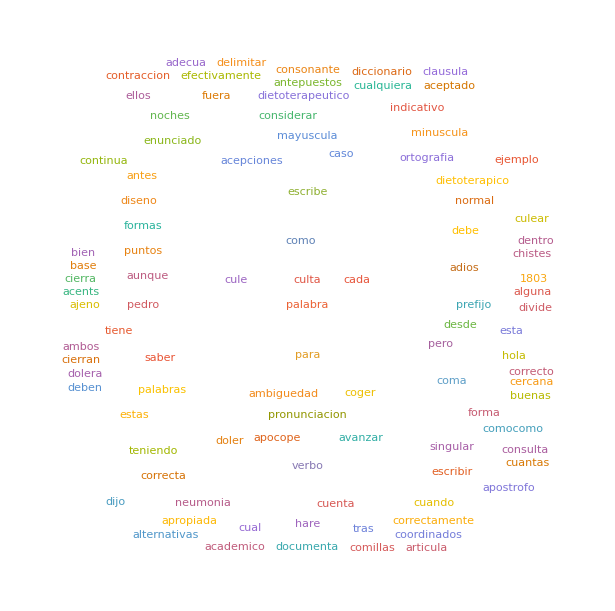

Luis Antonio Vasquez Reina

Enter department here

Enter date here

## Introducción

Twitter es una plataforma en línea donde los usuarios pueden publicar mensajes cortos (Tweets). Al enviar estos tweets (twittear), éstos son publicamente visibles no solo a los usuarios, sino también a cualquier visitante al sitio. Lo usuarios tienen la posibilidad de republicar (retwittear) un tweet, o de calificarlo (poniendo “Me gusta”). De esta manera, Twitter se ha convertido en una especie de foro mundial, donde además de personas comunes y corrientes, tienen presencia celebridades, académicos, activistas, instituciones, empresas, y gobiernos. Una de estas instituciones es la Real Academia de la lengua Española. Aparte de usar su cuenta de Twitter para divulgar sus eventos y publicaciones, la RAE acepta y responde las dudas lingüísticas que le envían los usuarios, naturalmente en su mayoría hispanoparlantes. La forma usual de enviar consultas a la RAE, es incluyendo la etiqueta (hashtag) #RAEconsultas, o más recientemente, #dudaRAE (a partir de Julio de 2019). Dado que Twitter no está restringido geográficamente, las consultas vienen tanto de hispanoparlantes de Madrid, como de CDMX, Buenos Aires, Malabo, Bogotá, Caracas, Miami, etc. Este trabajo trada de explorar las consciencias lingüísticas manifestadas en las consultas enviadas a la RAE. La metodología consiste en evaluar diferentes grupos de Tweets, todos enviados entre el 20  y 27 de junio de 2019: 

1. Tweets con el hashtag #RAEconsultas
2. Tweets respondidos por la RAE a consultas en #RAEconsultas
3. Tweets enviados a la RAE en general.

El estudio está basado en análisis estadísitico de frecuencias de palabras, y de ejemplos notables. Las secciones “Consiguiendo la data” y “Curando la data” solo usan una muestra pequeña del 14 de Junio de 2019, pues son ilustrativas. Toda la data obtenida para este trabajo está disponible a pedido.

## Consiguiendo la data

Me conecto a Twitter

```mathematica
twitter=ServiceConnect["Twitter","New"]
```

ServiceObject[…]

Obtengo la información de la cuenta de la RAE

```mathematica
RAE=First@twitter["UserData","Username"->"raeinforma"]
```

<|ID→350411337,ScreenName→RAEinforma,Name→RAE,Location→Madrid, España,FavouritesCount→910,FollowersCount→1410922,FriendsCount→156|>

```mathematica
RAE["ID"]
```

350411337

Esta es la ID que tiene la cuenta de la RAE en Twitter.
Ahora, consigo aproximadamente los últimos 200 Tweets bajo el hashtag #RAEconsultas

```mathematica
Tweets=twitter["TweetSearch","Query"->"#RAEconsultas",MaxItems->200]
```

Para filtrar los Tweets irrelevantes, solo me fijo en aquellos que tengan al menos 10 Retweets, es decir, aquellos que consiguieron un mínimo de atención por parte de los usuarios:

```mathematica
Tweets=twitter["TweetSearch","Query"->"#RAEconsultas",MaxItems->200]
```

Para saber quién twiteó cada uno de los tweets, necesitamos  los IDs de los Tweets

```mathematica
tweetsIDs=Normal@Tweets[[All,"ID"]];
(* El ";" al final de la instrucción hace que el resultado no se imprima en pantalla, 
pero de todas maneras es calculado *)
```

Así es como se ve la información del un Tweet, en este caso, el ejemplo será el primer Tweet de la tabla de arriba:

```mathematica
twitter["GetTweet","TweetID"->First[tweetsIDs]]
```

## “Curando” la data

Así se extrae información de un Tweet en particular, por ejemplo el rubro “Username”

```mathematica
twitter["GetTweet","TweetID"->First[tweetsIDs]]["Username"]
```

Samirtacos

Además, aparentemente hacer un Retweet “simple” (o sea, sin escribir nada más) crea un Tweet con un nuevo ID, pero con el mismo texto. Por esto, tengo que borrar los Tweets con texto duplicado:

```mathematica
Tweets=DeleteDuplicatesBy[#["Text"]&][Tweets]
```

```mathematica
tweetsIDs=Normal@Tweets[[All,"ID"]]; (*tiene que ser recalculado*)
```

Seleccionaré los Tweets que fueron publicados por la RAE. Para esto, tengo que recolectar la información de cada Tweet, y fijarme en el rubro “Username” . Las funciones implementadas “Select” y “SameQ” son útiles para esto:

```mathematica
Select[{1,2,3,"hola",88},EvenQ]
```

{2,88}

```mathematica
SameQ[5,2+ 0*1234567891 +3]
```

True

```mathematica
tweetsRAE=
Select[tweetsIDs,
      twitter["GetTweet","TweetID"->#]["Username"]== "RAEinforma"&]
      (*Demora de 1 a 2 minutos*)
```

{1139675207843700736,1139666970650075139}

```mathematica
(*Se puede verificar que de hecho son de la RAE en https://twitter.com/RAEinforma/status/1139675207843700736 *)
```

Con esto, los Tweets de los hablantes son el resto

```mathematica
tweetsNoRae=Complement[tweetsIDs,tweetsRAE]
```

{1139610348741386246,1139613374851866624,1139618072623493120,1139622281834053633,1139624712345198594,1139624734478557185,1139643667751346178,1139646220639621122,1139651203095310336,1139665129044434945,1139665714913185796,1139678886755807232,1139686645832114184,1139691289991979010,1139705560587210752,1139710740686725121,1139716143109701632,1139716271451201536,1139716473558056960,1139716847522050049,1139736122060357632,1139749751732129793,1139751570541703168,1139757861511278593,1139757876598042624,1139757965471207424,1139758892697751552}

Ahora, con un poco más de trabajo, construyo una tabla de los Tweets de los hablantes

```mathematica
tablaNoRae=Dataset@ (Normal@*(twitter["GetTweet","TweetID"->#]&) /@tweetsNoRae)
(*Demora de 1 a 2 minutos*)
```

Antes de comenzar a trabajar con el texto de los Tweets, hay que lidiar con que el formato del texto no es uniforme. 
La siguiente función ayuda con eso, eliminando símbolos especiales, tildes, puntuación, cambiando mayúsculas a minúsculas, etc. Para eliminar palabras que aumentan “ruido” a la data, esta función también elimina las palabras con longitudes de tres caracteres o menos (esto es fácil de cambiar y eliminar):

```mathematica
Clear[arreglarTexto];
arreglarTexto[texto_String]:=
Select[TextWords[#],StringLength[#]>3&]& @RemoveDiacritics@ToLowerCase@
StringReplace[texto,
{"#"~~Shortest[___]~~" "->"","#"~~Shortest[___]~~EndOfString->"","@"~~Shortest[___]~~" "->"",
"¡"->"","!"->"","¿"->"","?"->"","/"->"","\\"->"","."->"",":"->"",":"->"",
"-"->"","("->"",")"->"","«"->"","»"->""}]
(*elimina tildes, símbolos especiales, hashtags y menciones de usuario de twitter,
y devuelve la lista de palabras del tweet*)

arreglarTweet[texto_]:=RemoveDiacritics@ToLowerCase@
StringReplace[texto,
{"#"~~Shortest[___]~~" "->"","#"~~Shortest[___]~~EndOfString->"","@"~~Shortest[___]~~" "->"",
"¡"->"","!"->"","¿"->"","?"->"","/"->"","\\"->"","."->"",":"->"",":"->"",
"-"->"","("->"",")"->"","«"->"","»"->""}];
(*Igual que antes, pero devuelve el tweet completo*)
```

Se ve que funciona como planeado

```mathematica
arreglarTexto["asdf #asdf 12 hola"]
```

{asdf,hola}

```mathematica
arreglarTweet["asdf #asdf 12 hola"]
```

asdf 12 hola

Probando con un Tweet real:

```mathematica
arreglarTexto["@realDonaldTrump: I would like to extend my best #wishes to all, 
even the haters and losers, on this special date, September 11th."]
(*https://twitter.com/realdonaldtrump/status/377947866641485824*)
```

{would,like,extend,best,even,haters,losers,this,special,date,september,11th}

Se puede acceder al texto de un Tweet de la siguiente manera:

```mathematica
(tablaNoRae[[1]])["Text"]
(*por poner un ejemplo, veo el primero de la tabla*)
```

RT @SaninPazC: Caballeros (y escasas damas) de la @RAEinforma: ¿Por qué, si los hispanoparlantes americanos somos mucho más que los español…

La URL se obtiene de forma similar:

```mathematica
(tablaNoRae[[1]])["URL"]
```

URL[https://twitter.com/ALBE2010/status/1139610348741386246]

Un inconveniente, por ahora, es que el programa no se ha actualizado para trabajar con los nuevos Tweets de 280 caracteres:

```mathematica
StringLength[ (tablaNoRae[[4]])["Text"] ]
```

140

## Trabajando con la data

```mathematica
palabrasNoRae=Flatten@Normal[arreglarTexto[#["Text"]]&/@tablaNoRae]
```

Así se ve la lista de las palabras usadas en los ejemplos:

{caballeros,escasas,damas,hispanoparlantes,americanos,somos,mucho,espanol,adjetivos,terminaciones,como,rojo,amarillo,listo,espanol,reproduccion,risa,separando,elementos,repetidos,seguro,usted,sabe,contestarse,pregunta,pero,conjuncion,adversativa,atona,escrita,tilde,llame,vino,escritura,correcta,consejo,estado,grafia,apropiada,lengua,culta,unica,registrada,culear,participio,punto,escribe,siempre,despues,comillas,gusta,mucho,musica,recomienda,emplear,primera,instancia,comillas,latinas,reservando,inglesas,cuando,puto,emplea,como,prefijo,intensificador,propio,jerga,juvenil,espana,gramaticalmente,femenino,medico,medica,tanto,usos,adjetivos,consulta,medica,letra,como,supuesta,marca,genero,inclusivo,ajeno,morfolog,cualquiera,acepciones,verbo,coger,escriben,formas,aunque,pronunciacion,cercana,original,seria,spaiderman,menos,verbo,imprimir,tiene,participios,ambos,igualmente,correcto,acents,validas,mostrar,comocomo,avanzar,normal,considerar,palabra,hostia,escribe,todas,acepciones,oblea,misa,golpe,ordinales,coordinados,antepuestos,como,caso,sustantivo,puede,singular,pues,persona,singular,presente,indicativo,verbo,saber,efectivamente,entre,cada,sintagma,repetido,debe,escribirse,coma,tercero,desde,2010,guion,debe,escribirse,tilde,monosilabo,efectos,ortograficos,pues,espanol,actual,debe,evitarse,arcaico,adonde,donde,valor,movim,escribe,mayuscula,tras,puntos,suspensivos,ellos,cierra,enunciado,vinieron,luis,hijo,puta,forma,estandar,pero,hijueputa,valida,como,reflejo,pronunciaci,puntos,cierran,enunciado,tras,ellos,continua,minuscula,obstante,sentimos,pero,consulta,queda,fuera,limites,establecidos,para,este,servicio,esperam,apostrofo,cuando,produce,apocope,palabra,para}

Podemos hacer una nube de palabras de la lista, la cual toma en cuenta la frecuencia de la palabra

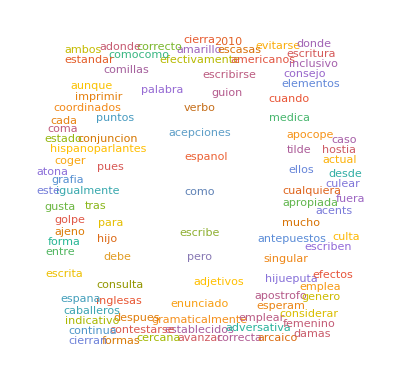

```mathematica
WordCloud[palabrasNoRae]
```

Para hacer un análisis más fino: podemos obtener la cantidad de menciones

```mathematica
Select[Counts[palabrasNoRae], #>1&]//Sort//Reverse//Dataset
```

Vemos que las palabras comunes en el ejemplo, tienen que ver con gramática y ortografía. Ahora, dejamos la data de ejemplo y pasamos a la data del 20 al 27 de junio

## Resultados

Tweets con el hashtag #RAEconsultas

Vemos los Tweets más retweeteados en este hastag.

```mathematica
(tweetsRAEConsultas[Select[#RetweetCount>100&]])
```

Podemos ver que estos tweets tienen que ver con consultas sobre uso y corrección. Es notable que la quinta parte tiene que ver con el lenguaje inclusivo. Además, hay tweets referentes a la cultura popular actual:

```mathematica
(tweetsRAEConsultas[Select[#RetweetCount>100&]])[All,{"Text"->arreglarTweet}][All,"Text"]//Normal//Column
```

rt lo sentimos, pero su consulta queda fuera de los limites establecidos para este servicio esperam…
rt cuando puto se emplea como prefijo intensificador uso propio de la jerga juvenil de espana y no r…
rt la voz tenis tiene la misma forma en singular el tenis que en plural los tenis
rt el uso de la letra e como supuesta marca de genero inclusivo es ajeno a…
rt la diferencia entre uwu y owo es que en la expresion facial que corresponde al pri…
rt el espanol ya tiene un mecanismo inclusivo el uso del masculino gramatical, que como termino no m…
rt la escritura correcta es consejo de estado
rt el diccionario academico de americanismos registra las grafias mamahuevo y mamaguevo
rt hijo de puta es la forma estandar, pero hijueputa es valida como reflejo de la pronunciacion c…
rt hay adjetivos de dos terminaciones, como rojo, ja, amarillo, lla o listo, ta…
rt efectivamente, entre cada sintagma repetido debe escribirse coma y va el tercero, y va el te…
rt el plural de pokemon seria pokemones
rt el uso de la letra e como supuesta marca de genero inclusivo es ajeno a la morfologia del espano…
rt aunque la pronunciacion mas cercana al original seria [spaiderman], al menos en e…
rt efectivamente, si se trata de la denominacion de un equipo deportivo, es valido el uso del articulo…

También podemos ver aquellos tweets que han recibido más “Me gusta”s

```mathematica
(tweetsRAEConsultas[Select[#FavoriteCount>100&]])
```

Estos tweets tienen una carga gramatical más notoria que los anteriores:

```mathematica
(tweetsRAEConsultas[Select[#FavoriteCount>100&]])[All,{"Text"->arreglarTweet}][All,"Text"]//Normal//Column
```

para que el enunciado no sea agramatical, debe mantenerse el pronombre relativo que tesis que para obtener el titulo [] presenta
la puntuacion correcta es estoy bien, y tu
cuando se desea expresar de forma sintetica la relacion que se establece entre las entidades designadas por dos sustantivos, se utiliza el guion relacion amorodio; binomio espaciotiempo
se recomienda usar en primera instancia las comillas angulares  , reservando las inglesas “ ” y las simples ‘ ’, en este orden, para entrecomillar partes de un texto ya entrecomillado para otros usos de las simples, v httpstcouc82pubm3k
sentimos desilusionarla, pero ese tuit no es de la cuenta oficial de sino de otra que, quiza con intencion de que se confunda con la nuestra, tiene un nombre parecido
la intencion es proporcionar orientacion normativa sobre el uso correcto del espanol
la puntuacion mas recomendable es quien escribia las glosas los reyes, los monjes o la gente del barrio
ambas el complemento introducido por a indica el destinatario que puede ser una oracion; el complemento con de, lo que se agradece tita siempre daba gracias a dios de que su mama solo se banara una vez por semana l esquivel
ordenes, plural del sust orden, lleva tilde porque es palabra esdrujula da ordenes claras ordenes, 2.aa del sing del presente de subjuntivo del verbo ordenar, no se tilda porque es palabra llana terminada en s espero que lo ordenes
mas es una conj adversativa [= pero] atona escrita sin tilde le llame, mas no vino en el resto de los casos, mas se escribe con tilde como cuantificador mas lejos; mas frio, como sustantivo pon un mas, en la loc adv mas bien
lo sentimos, pero su consulta no plantea una duda linguistica, sino de interpretacion de la realidad esperamos poder serle de utilidad en otra ocasion
las dos son validas la forma halar es la originaria y en ella la h es muda en el espanol estandar, pero en algunas zonas se aspira esa aspiracion generalizada ha trascendido a la escritura, dando lugar a la variante jalar, tambien correcta
la palabra luis se escribe sin tilde en espanol porque es monosilaba y los monosilabos se escriben siempre sin tilde sol, bien, la, fui, ven, di a excepcion de los casos de monosilabos con tilde diacritica tutu, elel, dede, sisi

Ahora, vemos las palabras más comunes de esta categoría:

```mathematica
Flatten[arreglarTexto/@(Normal@tweetsRAEConsultas[All,"Text"])]//Counts//Sort//Reverse//Dataset
```

```mathematica
Flatten[arreglarTexto/@(Normal@tweetsRAEConsultas[All,"Text"])]//Counts//Sort//Reverse//Normal//Take[#,50]&
```

{como→356,para→302,debe→212,pero→162,forma→161,espanol→156,consulta→154,puede→146,ella→143,esta→143,disculpe→124,etiqueta→122,responder→120,podamos→119,incluir→118,molestias→113,correcto→112,sobre→108,palabra→101,este→100,diccionario→96,correcta→96,verbo→93,tilde→89,solo→87,cuando→86,gracias→75,usar→71,tiene→70,aunque→69,vease→66,tambien→63,porque→62,validas→60,ejemplo→57,caso→56,decir→56,normal→54,tanto→54,nombre→53,coma→51,sustantivo→50,lengua→50,dudas→49,escribe→49,valido→49,escribirse→48,cual→48,ambas→47,otra→46}

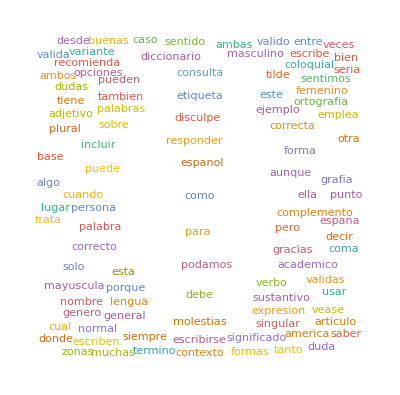

```mathematica
Flatten[arreglarTexto/@(Normal@tweetsRAEConsultas[All,"Text"])]//WordCloud
```

Tweets respondidos por la RAE a #RAEconsultas

```mathematica
(tweetsRAEConsultasEnviadosPorRAE[Select[#RetweetCount>100&]])
```

```mathematica
(tweetsRAEConsultasEnviadosPorRAE[Select[#FavoriteCount>100&]])
```

Comparando con la sección anterior, vemos que los Tweets enviados por la RAE son los mejor calificados bajo este hashtag, pues se repiten varios tweets:

```mathematica
(tweetsRAEConsultasEnviadosPorRAE[Select[#FavoriteCount>100&]])[All,{"Text"->arreglarTweet}][All,"Text"]//Normal//Column
```

para que el enunciado no sea agramatical, debe mantenerse el pronombre relativo que tesis que para obtener el titulo [] presenta
la puntuacion correcta es estoy bien, y tu
cuando se desea expresar de forma sintetica la relacion que se establece entre las entidades designadas por dos sustantivos, se utiliza el guion relacion amorodio; binomio espaciotiempo
se recomienda usar en primera instancia las comillas angulares  , reservando las inglesas “ ” y las simples ‘ ’, en este orden, para entrecomillar partes de un texto ya entrecomillado para otros usos de las simples, v httpstcouc82pubm3k
sentimos desilusionarla, pero ese tuit no es de la cuenta oficial de sino de otra que, quiza con intencion de que se confunda con la nuestra, tiene un nombre parecido
la intencion es proporcionar orientacion normativa sobre el uso correcto del espanol
la puntuacion mas recomendable es quien escribia las glosas los reyes, los monjes o la gente del barrio
ambas el complemento introducido por a indica el destinatario que puede ser una oracion; el complemento con de, lo que se agradece tita siempre daba gracias a dios de que su mama solo se banara una vez por semana l esquivel
ordenes, plural del sust orden, lleva tilde porque es palabra esdrujula da ordenes claras ordenes, 2.aa del sing del presente de subjuntivo del verbo ordenar, no se tilda porque es palabra llana terminada en s espero que lo ordenes
mas es una conj adversativa [= pero] atona escrita sin tilde le llame, mas no vino en el resto de los casos, mas se escribe con tilde como cuantificador mas lejos; mas frio, como sustantivo pon un mas, en la loc adv mas bien
lo sentimos, pero su consulta no plantea una duda linguistica, sino de interpretacion de la realidad esperamos poder serle de utilidad en otra ocasion
las dos son validas la forma halar es la originaria y en ella la h es muda en el espanol estandar, pero en algunas zonas se aspira esa aspiracion generalizada ha trascendido a la escritura, dando lugar a la variante jalar, tambien correcta
la palabra luis se escribe sin tilde en espanol porque es monosilaba y los monosilabos se escriben siempre sin tilde sol, bien, la, fui, ven, di a excepcion de los casos de monosilabos con tilde diacritica tutu, elel, dede, sisi

Ahora, vemos las palabras más comunes de esta categoría:

```mathematica
Flatten[arreglarTexto/@(Normal@tweetsRAEConsultasEnviadosPorRAE[All,"Text"])]//Counts//Sort//Reverse//Dataset
```

```mathematica
Flatten[arreglarTexto/@(Normal@tweetsRAEConsultasEnviadosPorRAE[All,"Text"])]//Counts//Sort//Reverse//Normal//Take[#,50]&
```

{para→230,como→218,debe→169,consulta→136,ella→128,disculpe→114,etiqueta→111,molestias→110,incluir→110,responder→110,podamos→110,puede→109,espanol→108,pero→105,forma→96,sobre→94,esta→80,diccionario→79,este→74,tilde→67,solo→62,verbo→59,palabra→56,vease→56,correcto→53,tambien→50,cuando→49,tiene→49,correcta→47,aunque→47,tanto→45,usar→45,validas→43,porque→42,normal→42,caso→41,lengua→41,academico→39,otra→39,nombre→39,dudas→38,sustantivo→37,valido→37,sentido→33,femenino→32,escribirse→32,ambas→32,variante→32,sentimos→31,america→30}

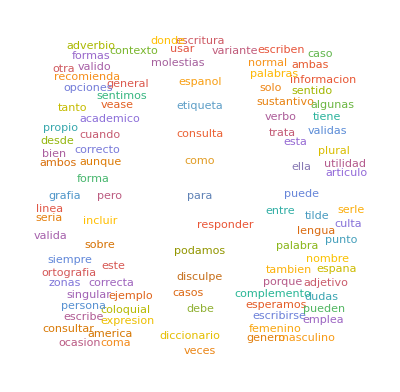

```mathematica
Flatten[arreglarTexto/@(Normal@tweetsRAEConsultasEnviadosPorRAE[All,"Text"])]//WordCloud
```

Tweets enviados a la RAE en general

Como la mayoría de los Tweets enviados son ignorados, por eso tuve que bajar la valla de 100 a 10

```mathematica
(tweetsRAERecibidos[Select[#RetweetCount>10&]])
```

```mathematica
(tweetsRAERecibidos[Select[#RetweetCount>10&]])[All,{"Text"->arreglarTweet}][All,"Text"]//Normal//Column
```

rt por que aparece la misma definicion para consolador y vibrador si tienen acepciones tan diferentes uno del otro…
rt calor que te torras
rt  cual seria el termino adecuado para definir una desmedida preferencia que algunos dan a sus amistades o conocido…
 cual seria el termino adecuado para definir una desmedida preferencia que algunos dan a sus amistades o conocidos

```mathematica
(tweetsRAERecibidos[Select[#FavoriteCount>10&]])
```

Vemos que las consultas hechas son muy coloridas, pero muestran partes interesantes de sus consciencias lingüísticas:
- Lo que consideran curiosidades del español
- Consciencia de diferentes modos de hablar en otros lugares
- Humor lingüístico
- Preocupación por la corrección
- “Etimología”

```mathematica
(tweetsRAERecibidos[Select[#FavoriteCount>10&]])[All,{"Text"->arreglarTweet}][All,"Text"]//Normal//Column
```

estos vatos siempre andan al tiro, gracias httpstco31oxcmc3qf
calor del culo
vease este ejemplo
"te ordeno que ordenes las ordenes de produccion"
buenos dias
ustedes le ponen la bandera de colombia a la palabra "chicharrera" para referirse al intenso calor me sorprende, porque yo la llevo oyendo y empleando toda mi vida en sesena toledo, y juraria que se emplea en el resto de castilla al menos
culesolhijueputa
nos permiten decir "que calor tan alvaro uribe", para referirnos al tradicional "que calor tan hijueputa"  gracias, son un sol🌞
en manchego hay algunos ejemplos y me dejo alguno, seguro
caloruzo
rechisquero &lt;rechijquero&gt;
calentin
solanera
solarrera
la calor
asaero

hola a partir de ahora hay que anadir esa etiqueta ademas de mencionaros gracias 
httpstcoj7eun1q1mv
 cual seria el termino adecuado para definir una desmedida preferencia que algunos dan a sus amistades o conocidos 
pero si puso el hashtag😂
es que homo en este caso no viene del latin "homo, hominis ", sino del griego "homoios", que significa el mismo hetero viene tambien del griego "heteros ", que significa el otro si no hubieran extirpado las clasicas,  nuestro espanol mejoraria

Ahora, vemos las palabras más comunes de esta categoría, parece que la gente aprecia los modales:

```mathematica
Flatten[arreglarTexto/@(Normal@tweetsRAERecibidos[All,"Text"])]//Counts//Sort//Reverse//Dataset
```

```mathematica
Flatten[arreglarTexto/@(Normal@tweetsRAERecibidos[All,"Text"])]//Counts//Sort//Reverse//Normal//Take[#,50]&
```

{gracias→425,como→282,para→194,esta→190,correcto→184,palabra→182,cual→158,correcta→135,pero→129,decir→127,calor→108,dice→108,muchas→106,hola→101,duda→89,cuando→86,forma→84,seria→84,bien→82,ejemplo→76,tengo→71,puede→71,este→62,buenas→60,verbo→58,escribir→56,frase→54,caso→49,espanol→48,pregunta→48,respuesta→47,saber→47,existe→47,debe→46,tiene→46,siempre→45,consulta→45,dias→44,tardes→44,favor→44,solo→44,tambien→41,escribe→41,algo→39,usar→39,termino→38,tilde→37,porque→36,hace→34,esto→33}

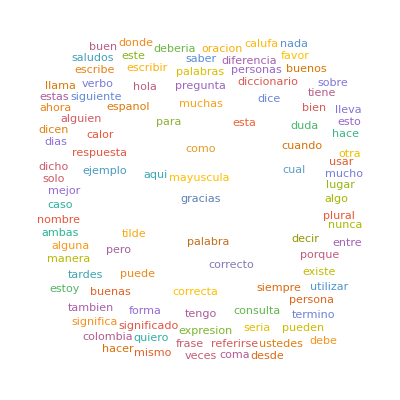

```mathematica
Flatten[arreglarTexto/@(Normal@tweetsRAERecibidos[All,"Text"])]//WordCloud
```

## Conclusiones:

Resumen: Lo que ya sabíamos, pero basado en evidencia.

La alta frecuencia de las palabras como “como(cómo)”, “correcto”, “consulta”, ”palabra”,”diccionario”, “puede”,”pronunciación”, ”forma”, “debe”, “verbo”, etc. tanto entre los envíos a la RAE como en las respuestas de la RAE, sugiere que hay un diálogo entre los usuarios y la RAE, donde los temas principales son el “buen uso” y la “correción” del idioma español. El hecho de que esto sea hecho por medio de consultas, muestra que es un diálogo mayoritariamente unidireccional, en que los hablantes aceptan la autoridad de la RAE sobre estos temas. Por otro lado, el hecho de que este fenómeno siquiera exista, apoya la existencia de la consciencia lingüística y de sus límites, por ejemplo en el caso del lenguaje inclusivo (i.e., si fuera una decisión clara, no se haría la consulta).

#### Ventajas

- Este experimento es fácilmente reproducible y reescalable
- Bajo costo
- Fácilmente podrían modificarse las instrucciones para obtener otras características de la data, por ejemplo, momento de publicación
- Independencia del marco teórico.

#### Desventajas y limitaciones

- Este programa ignora puntuación, así, palabras como “cómo”, “como” (conjunción) y “como” (comer) son contadas como la misma, además, se colan las URLs.
- Este programa solo puede trabajar con los primeros 140 caracteres de un Tweet, aún le falta actualizarse.
- Solo estamos registrando a aquellos que tengan acceso a internet, lo cual no está distribuído uniformemente en el mundo hispanohablante.
- Falta mejorar los métodos para eliminar información irrelevante (conectores, spam)
- Twitter limita la información disponible a entidades externas, e.g, para la geolocalización solo contamos con el testimonio de los usuarios; el nivel educativo no es accesible

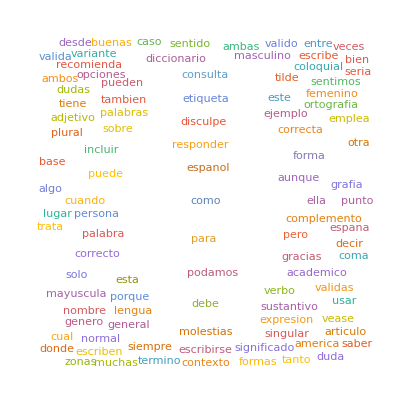
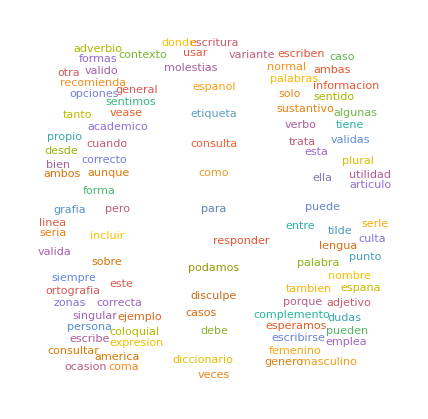
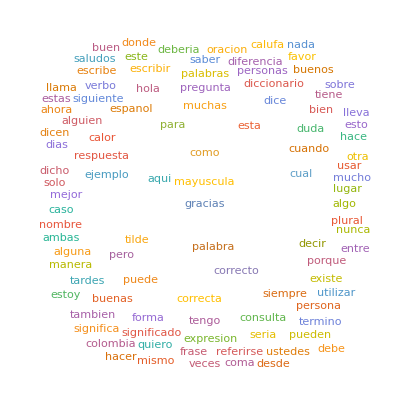

```mathematica
(*Module[{temporalRAEConsultas,temporalRAERecibidos, nuevosConsultasIDSRAE},
(*VER LOS IMPORTS ABAJO DE ESTE MODULE*)

Clear[arreglarTexto];
arreglarTexto[texto_String]:=
Select[TextWords[#],StringLength[#]>3&]& @RemoveDiacritics@ToLowerCase@
StringReplace[texto,
{"#"~~Shortest[___]~~" "->"","#"~~Shortest[___]~~EndOfString->"","@"~~Shortest[___]~~" "->"",
"¡"->"","!"->"","¿"->"","?"->"","/"->"","\\"->"","."->"",":"->"",":"->"",
"-"->"","("->"",")"->"","«"->"","»"->""}];
(*elimina tildes, símbolos especiales, hashtags y menciones de usuario de twitter *)

Clear[ConseguirPalabras];
ConseguirPalabras[dataset_]:=Flatten@Normal[arreglarTexto[#["Text"]]&/@dataset];


tweetsRAEConsultas=twitter["TweetSearch","Query"->"#RAEconsultas",MaxItems->200];
tweetsRAERecibidos=twitter["TweetSearch","Query"->"to:RAEinforma",MaxItems->200];
RAEConsultasIDS=Normal@tweetsRAEConsultas[[All,"ID"]];
RAEConsultasIDSRAE=Select[RAEConsultasIDS,
      twitter["GetTweet","TweetID"->#]["Username"]== "RAEinforma"&];
RAEConsultasIDSNoRAE=Complement[RAEConsultasIDS,RAEConsultasIDSRAE];
tweetsRAEConsultasEnviadosPorRAE=tweetsRAEConsultas[Select[MemberQ[RAEConsultasIDSRAE,#ID]&]];

limite=10;
Print[Now+limite*LinguisticAssistant];

For[i=0,i<limite,i++,
temporalRAEConsultas= twitter["TweetSearch","Query"->"#RAEconsultas",MaxItems->400];
temporalRAERecibidos=twitter["TweetSearch","Query"->"to:RAEinforma",MaxItems->400];
tweetsRAEConsultas=DeleteDuplicatesBy[Dataset@Join[Normal@tweetsRAEConsultas,Normal@temporalRAEConsultas],#["Text"]&];
tweetsRAERecibidos=DeleteDuplicatesBy[Dataset@Join[Normal@tweetsRAERecibidos,Normal@temporalRAERecibidos],#["Text"]&];
RAEConsultasIDS=DeleteDuplicates@Join[RAEConsultasIDS,Normal@temporalRAEConsultas[[All,"ID"]]  ];

Print["Comienza a buscar los tweets de #RAEconsultas que fueron enviados por la RAE \n"];
nuevosConsultasIDSRAE=Select[   Normal@temporalRAEConsultas[[All,"ID"]] , twitter["GetTweet","TweetID"->#]["Username"]== "RAEinforma"& ];

RAEConsultasIDSRAE=DeleteDuplicates@Join[RAEConsultasIDSRAE,   nuevosConsultasIDSRAE                  ];
RAEConsultasIDSNoRAE=Complement[RAEConsultasIDS,RAEConsultasIDSRAE];

tweetsRAEConsultasEnviadosPorRAE            =DeleteDuplicatesBy[tweetsRAEConsultas[Select[MemberQ[RAEConsultasIDSRAE     ,#ID]&]],#["Text"]&];
tweetsRAEConsultasEnviadosPorUsuarios=DeleteDuplicatesBy[tweetsRAEConsultas[Select[MemberQ[RAEConsultasIDSNoRAE ,#ID]&]],#["Text"]&];

(*estas variables se basan en los datasets. Si cambian los datasets, cambian las palabras. Luego tengo que hacer un Join!*)
palabrasRAEconsultas=ConseguirPalabras[tweetsRAEConsultas];
palabrasRAERecibidos=ConseguirPalabras[tweetsRAERecibidos];
palabrasRAEconsultasEnviadasPorRAE=ConseguirPalabras[tweetsRAEConsultasEnviadosPorRAE];
palabrasRAEconsultasEnviadasPorUsuarios=ConseguirPalabras[tweetsRAEConsultasEnviadosPorUsuarios];

NotebookSave[];
(*Con los siguientes Exports nos aseguramos de no perder la data*)
Export["E:\\Google Drive\\Semestre actual\\Historia del español 2\\Trabajo Twitter\\palabrasRAEconsultas.txt",StringRiffle[palabrasRAEconsultas,"\n"],"Text"];
Export["E:\\Google Drive\\Semestre actual\\Historia del español 2\\Trabajo Twitter\\palabrasRAERecibidos.txt",StringRiffle[palabrasRAERecibidos,"\n"],"Text"];
Export["E:\\Google Drive\\Semestre actual\\Historia del español 2\\Trabajo Twitter\\palabrasRAEconsultasEnviadasPorRAE.txt",StringRiffle[palabrasRAEconsultasEnviadasPorRAE,"\n"],"Text"];
Export["E:\\Google Drive\\Semestre actual\\Historia del español 2\\Trabajo Twitter\\palabrasRAEconsultasEnviadasPorUsuarios.txt",StringRiffle[palabrasRAEconsultasEnviadasPorUsuarios,"\n"],"Text"];
Print["LLegó a justo antes de hacer un Pause\n"];
Pause[LinguisticAssistant];
Print["Ya pasó un Pause\n"];
];
NotebookSave[];
]
```